```mathematica
DSolve [y'[x]==Sin[5x],y[x],x]
```

{{y[x]→C[1]-1/5 Cos[5 x]}}

```mathematica
DSolve [x^2*y'[x]==y[x]-y[x]*x,y[x],x]
```

{{y[x]→(ⅇ^(-1/x) C[1])/x}}

```mathematica
DSolve [{x^2*y'[x]==y[x]-y[x]*x,y[1]==1/E},y[x],x]
```

{{y[x]→ⅇ^(-1/x)/x}}

```mathematica
DSolve[{y''[x]+5*y'[x]+2*y[x]==0,y[0]==5,y'[0]==10},y[x],x]
```

{{y[x]→-5/34 (-17 ⅇ^((-5/2-(√17)/2) x)+9 √17 ⅇ^((-5/2-(√17)/2) x)-17 ⅇ^((-5/2+(√17)/2) x)-9 √17 ⅇ^((-5/2+(√17)/2) x))}}

```mathematica
a=NDSolve[{y''[x]+x*y[x]==0,y[0]==1,y[1]==1},y,{x,0,10}]
```

{{y→InterpolatingFunction[{{0.,10.}},<>]}}

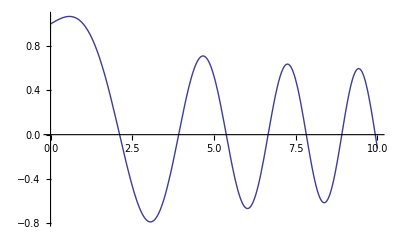

```mathematica
Plot[Evaluate[y[x]/.a],{x,0,10}]
```

```mathematica
a=DSolve[{y''[t]+(y[t]+1)^2*y'[t]+y[t]==0,y[t]==1,y'[0]==0},y,{t,0,10}]
```

DSolve::dsvar: 0 cannot be used as a variable.

DSolve[{y[t]+(1+y[t])^2 y'[t]+y''[t]==0,y[t]==1,y'[0]==0},y,{t,0,10}]

```mathematica
b=NDSolve[{y''[t]+(y'[t]+1)^2*y'[t]+y[t]==0,y[0]==1,y'[0]==0},y,{t,0,10}]
```

{{y→InterpolatingFunction[{{0.,10.}},<>]}}

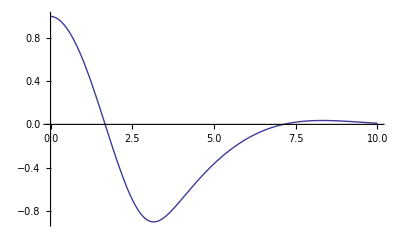

```mathematica
Plot[Evaluate[y[t]/.b],{t,0,10}]
```

```mathematica
c=NDSolve[{y''[x]+0.3*y'[x]+Sin[y[x]]==0,y[0]==2,y'[0]==0},y,{x,0,30}]
```

{{y→InterpolatingFunction[{{0.,30.}},<>]}}

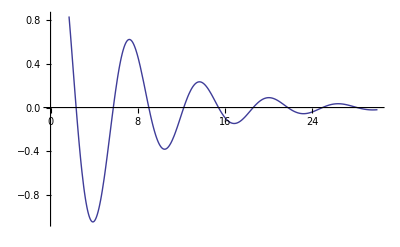

```mathematica
Plot[Evaluate[y[x]/.c],{x,0,30}]
```

```mathematica
DSolve[L*Q''[t]+R*Q'[t]+Q[t]/C==V*E^(j*w*t),Q[t],t]
```

```mathematica
i={{Q[t]->-(2 C L V (√C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) R-√C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) R+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) √(-4 L+C R^2)+ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) √(-4 L+C R^2)+2 √C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) j L w-2 √C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) j L w))/(√(-4 L+C R^2) (-√C R+√(-4 L+C R^2)-2 √C j L w) (√C R+√(-4 L+C R^2)+2 √C j L w))+ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)) C[1]+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)) C[2]}}
```

```mathematica
i={{Q[t]->-(2 C L V (√C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) R-√C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) R+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) √(-4 L+C R^2)+ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) √(-4 L+C R^2)+2 √C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) j L w-2 √C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) j L w))/(√(-4 L+C R^2) (-√C R+√(-4 L+C R^2)-2 √C j L w) (√C R+√(-4 L+C R^2)+2 √C j L w))+ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)) C[1]+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)) C[2]}}
```

{{Q[t]→-(2 C L V (√C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) R-√C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) R+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) √(-4 L+C R^2)+ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) √(-4 L+C R^2)+2 √C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) j L w-2 √C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) j L w))/(√(-4 L+C R^2) (-√C R+√(-4 L+C R^2)-2 √C j L w) (√C R+√(-4 L+C R^2)+2 √C j L w))+ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)) C[1]+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)) C[2]}}

```mathematica
D[i,t]
```

{{Q'[t]→-(2 C L V (√C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) R ((-C R+√C √(-4 L+C R^2))/(2 C L)+(R-(√(-4 L+C R^2))/(√C)+2 j L w)/(2 L))+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) √(-4 L+C R^2) ((-C R+√C √(-4 L+C R^2))/(2 C L)+(R-(√(-4 L+C R^2))/(√C)+2 j L w)/(2 L))+2 √C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) j L w ((-C R+√C √(-4 L+C R^2))/(2 C L)+(R-(√(-4 L+C R^2))/(√C)+2 j L w)/(2 L))-√C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) R ((-C R-√C √(-4 L+C R^2))/(2 C L)+(R+(√(-4 L+C R^2))/(√C)+2 j L w)/(2 L))+ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) √(-4 L+C R^2) ((-C R-√C √(-4 L+C R^2))/(2 C L)+(R+(√(-4 L+C R^2))/(√C)+2 j L w)/(2 L))-2 √C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) j L w ((-C R-√C √(-4 L+C R^2))/(2 C L)+(R+(√(-4 L+C R^2))/(√C)+2 j L w)/(2 L))))/(√(-4 L+C R^2) (-√C R+√(-4 L+C R^2)-2 √C j L w) (√C R+√(-4 L+C R^2)+2 √C j L w))+(ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)) (-C R-√C √(-4 L+C R^2)) C[1])/(2 C L)+(ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)) (-C R+√C √(-4 L+C R^2)) C[2])/(2 C L)}}